### Initialization of global variables and importing important structures

```mathematica
(* SET HERE THE WORKING DIRECTORY *)
SetDirectory["C:\\Users\\heikkie13\\Work\\howard_scratches\\Mathematica"];
<<libs/FunctionsComplexAnalysis.m;
<<libs/FunctionsMatrixAnalysis.m;
<<libs/FunctionsFiniteGroups.m;
<<libs/FunctionsGF2.m
<<libs/FunctionsForExtraSpeciality.m;

(* This is needed for the unitary reps of symplectivc matrices: *)
(* <<"SymplecticBinary.m"; *)

(*Clear[AllBinMats];*)
dB = 10*Log[10,N[#]]&;
Clear[mm,rr];
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

```mathematica
(* These are needed for functions to work properly *)
(* The dimension for the simulation must be chosen here, as multiple data structures neede by decoders etc depend on m*)
mm = 3; Nn= 2^mm; InxBin= Tuples[{0,1},{mm}]; WHn = WHmatrix[Nn]/Sqrt[Nn];  InitializeVeryBare[mm];
ZeroVecm = Table[0,{mm}];
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

### Codebook

```mathematica
GenerateChirp = Module[{Sint, bvec,xvec},Sint = #1; bvec = #2;
(xvec  = IntegerDigits[#-1,2,mm];
I^(xvec.Sint.xvec + 2 bvec.xvec)/Sqrt[2^mm]) &/@ Range[2^mm]
]&;

MakeUnitaryFromSymmetric = Module[{Sint,cvec,dvec,Ord2},Sint = #;
 (cvec = IntegerDigits[#-1,2,mm];
Ord2 = cvec.Sint.cvec;
(dvec  = IntegerDigits[#-1,2,mm];
I^(Ord2 + 2 dvec.cvec)/Sqrt[2^mm]
) &/@ Range[2^mm]
) &/@ Range[2^mm] ]&; 

AllBinSymm = GenerateSn2[mm];
AllUmats = MakeUnitaryFromSymmetric[#] &/@ AllBinSymm;
AllUmats // mfl;
CB  = Transpose[Sequence@@(Transpose[#]) &/@ AllUmats]; card = Length[CB[[1]]]; {Length[AllUmats],card}
```

{64,512}

#### Extended codebook

```mathematica
(* Creates upper triangular matrix from vector *)
upperTriangular[v_]:=upperTriangular[v,(1+Sqrt[1+8*Length@v])/2]
upperTriangular[v_,n_]:=Module[{i=0},Array[If[#>=#2,0,v[[++i]]]&,{n,n}]]
upperTriangulizer[n_Integer,type_:_Integer]:=Module[{v,r},Quiet[With[{r=upperTriangular[v,n]},Compile[{{v,type,1}},r]],Part::partd]]
(* Example printed below *)
upperTriangulizer[3] @ Range[3] // MatrixForm

(* Generates the set of (size X size) symmetric matrices with binary diagonal and off-diagonal elements belong to {0, 1/2, 1, 3/2} *)
ExtendedSymmetricMats=Module[{size, diag, diagmat, triuvec, triumat, result, results, inx},size=#;
results={};
(inx=#;
diag=IntegerDigits[Mod[inx,2^size],2,size];
diagmat=DiagonalMatrix[diag];
triuvec=IntegerDigits[Floor[inx/(2^size)],4, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat]+diagmat;
AppendTo[results,result];)&/@Range[0,2^(size^2)-1];
results
]&;
```

(0 | 1 | 2
0 | 0 | 3
0 | 0 | 0)

```mathematica
ExtendedSmats = ExtendedSymmetricMats[mm]; ExtendedSmats // mfl;
ExtendedUmats = MakeUnitaryFromSymmetric[#] &/@ ExtendedSmats; ExtendedUmats //mfl;
(* The matrices are unitary in the extended set *)
Union[MapThread[Dot, {ExtendedUmats,(ConjugateTranspose[#] &/@ ExtendedUmats)}]] //mfl
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
ExtendedCB  = Transpose[Sequence@@(Transpose[#]) &/@ ExtendedUmats];card = Length[ExtendedCB[[1]]]; {Length[ExtendedUmats],card}
```

{512,4096}

#### Minimal distances

```mathematica
(* WARNING, THIS IS INTENSIVE TO CALCULATE FOR mm > 2 *)
(* UNCOMMENT TO RUN *)

(*
innerprods = ConjugateTranspose[ExtendedCB].ExtendedCB; 
chorddists = Sqrt[1 - Abs[innerprods]^2];
chorddistflatten = chorddists // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Extended codebook has minimal chordal distance: ",FullSimplify[Min[Complement[chorddistflatten, {0}]]], " ≈ " , Min[Complement[chorddistflatten, {0}]] // N ]

innerprodsOrig = ConjugateTranspose[CB].CB; 
chorddistsOrig = Sqrt[1 - Abs[innerprodsOrig]^2];
chorddistflattenOrig = chorddistsOrig // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Vanilla BC codebook has minimal chordal distance: ", Min[Complement[chorddistflattenOrig, {0}]], " ≈ ", Min[Complement[chorddistflattenOrig, {0}]]// N ]
*)
```

### Decoders

#### Extended decoders

```mathematica
ExtendedDecoder=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest},vecin=#; 
squared=vecin*vecin;
squared=squared/Norm[squared];
{Sest, best, zleft,  metric}=BreadthFirstDecoding[squared,1, True, Range[mm]];
MaskS=Sest/2 + DiagonalMatrix[best];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, best, zleft,  metric}=BreadthFirstDecoding[UnmaskedChirp, 1, True, Range[mm]];
{Sest+MaskS,best}]&;

ExtendedDecoderBf=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest, SquaredCandidates, BaseChirpCandidates, Candidates, Shat, bhat, zhat, metrichat, Peakinxs},vecin=#1; K = #2;
squared=vecin*vecin;
squared=squared/Norm[squared];
SquaredCandidates=BreadthFirstDecodingGiveList[squared,K, True, Range[mm]];
Candidates = {};
( {Shat, bhat, zhat, metrichat} = #;
MaskS=Shat/2 + DiagonalMatrix[bhat];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
BaseChirpCandidates = BreadthFirstDecodingGiveList[UnmaskedChirp, K, True, Range[mm]]; 
({Sest, best, zleft, metric}=#;
AppendTo[Candidates, {Sest+MaskS,best,zleft,metric}];)&/@ BaseChirpCandidates;
)&/@ SquaredCandidates;
Peakinxs = Reverse[Ordering[Candidates[[All, 4]]]];
Candidates[[Peakinxs[[1]]]]
]&;

ExtendedDecoderBfPlus=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest, SquaredCandidates, BaseChirpCandidates, Candidates, Shat, bhat, zhat, metrichat, Peakinxs},vecin=#1; K = #2;
squared=vecin*vecin;
squared=squared/Norm[squared];
SquaredCandidates=BreadthFirstDecodingGiveList[squared,K, True, Range[mm]];
Candidates = {};
( {Shat, bhat, zhat, metrichat} = #;
MaskS=Shat/2 + DiagonalMatrix[bhat];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
BaseChirpCandidates = BreadthFirstDecodingGiveList[UnmaskedChirp, K, True, Range[mm]]; 
({Sest, best, zleft, metric}=#;
AppendTo[Candidates, {Sest+MaskS,best,zleft,metric+metrichat}];)&/@ BaseChirpCandidates;
)&/@ SquaredCandidates;
Peakinxs = Reverse[Ordering[Candidates[[All, 4]]]];
Candidates[[Peakinxs[[1]]]]
]&;

ExtendedDecoderBfBestBoth=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest, SquaredCandidates, BaseChirp, Candidates, Shat, bhat, zhat, metrichat, Peakinxs},vecin=#1; K = #2;
squared=vecin*vecin;
squared=squared/Norm[squared];
{Shat, bhat, zleft, metric}=BreadthFirstDecoding[squared,K, True, Range[mm]];
Candidates = {};
MaskS=Shat/2 + DiagonalMatrix[bhat];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, best, zleft, metric} = BreadthFirstDecoding[UnmaskedChirp, K, True, Range[mm]];
{Sest +MaskS, best, zleft, metric}
]&;
```

#### Truth table calculators and decoding order

```mathematica
DecodingOrder = Module[{vecin, maxis, PermMatEsh, abses, permutetable, inx}, vecin = #;
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
Reverse[Ordering[maxis]]
]&;

GiveTruthTable = Module[{index, size, basetable, binary}, input=#;
index = #1;
size = #2;
binary = Mod[Floor[(Range[2^size] - 1) / 2^(size -index)], 2];
Table[binary[[i]] == 0, {i, 1, 2^size}]
]&;

UpdateTruthTable = Module[{Tt,Tt2, R},
Tt = #1;
R = #2;
Tt2 = GiveTruthTable[R, mm];
Table[Tt[[i]] && Tt2[[i]], {i, 1, Length[Tt]}]
]&;
```

#### Row decoders

```mathematica
DecodeRowList = Module[{start, PauliMat, Metrics, Results, Projectedvectors, Peaks, Peaki, Peakinxs, Sestk, Metrick, Signbitsall, projectedvectors, Sests, Sest, R, K, RangeNow, Tt, vecrot, NewK,  Signbits, Svec, Signbitsk, Sigmak, veck, Mu, WithProjections, avec, bvec, PhaseVec, PermMatEsh, Wht, vecin, Abses, Signs},
Sest = #1;
Signbits = #2;
vecin = #3;
Mu = #4;
Tt = #5;
WithProjections = #6;
K = #7;
R = #8;
start = Transpose[Sest][[R]];
RangeNow=Pick[Range[2^mm],Tt] + FromDigits[start,2];
(* In the end K might be greater than the number of possible different rows *)
NewK = Min[K, Length[RangeNow]];
(* This normalizes out the phase i^{e_i.S.e_i^T} *)
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
PermMatEsh =  PermMatEShifts[[R]];
Wht =  Sqrt[Nn]PhaseVec*DiscreteHadamardTransform[Conjugate[vecin]*(PermMatEsh.vecin), Method->"BitComplement"] // Chop;
Abses = Abs[Wht];
Signs = Sign[Wht];
Metrics = {};
Signbitsall = {};
Projectedvectors = {};
Sests = {};

Peakinxs = Take[Select[Reverse[Ordering[Abses]], MemberQ[RangeNow, #]&], NewK];
Results = (
Peaki = #;
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;
If[WithProjections, Metrick = (Mu + Abses[[Peaki]]) / 2;, Metrick = (Mu + Abses[[Peaki]]);];
Sigmak = Signs[[Peaki]];
Signbitsk = Signbits; 
Signbitsk[[R]] =(1 - Sigmak) / 2;
Svec  = IntegerDigits[Peaki-1,2,mm];
Sestk[[R]]=Svec;
If[WithProjections, avec = ZeroVecm; avec[[R]]=1;
PauliMat = MakePauli[avec,Svec];
vecrot = vecin.PauliMat;
veck = (vecin + Sigmak * vecrot) / 2;
, 
(* This runs if withProjections = False *)
veck = vecin;
];
{Sestk, Signbitsk,veck, Metrick}
)&/@ Peakinxs;
Results
]&;
```

#### List decoder

```mathematica
BreadthFirstDecoding = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates, vecest, inners, cvec, best},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowList @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];

If[WithProjections, posi = 1, inners = (best = #[[2]]; Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[vecin].vecest]
) &/@ Candidatelist;
posi = Position[inners,Max[inners]][[1,1]]; ];
Candidatelist[[posi]]
]&;

BreadthFirstDecodingGiveList = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates, vecest, inners, cvec, best},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowList @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];
Candidatelist
]&;
```

### Simulation

#### Quantization simulation

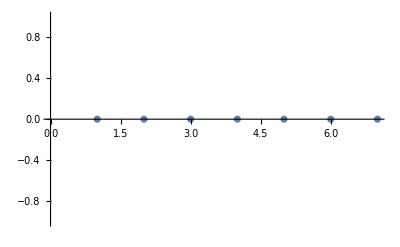

```mathematica
drops = 1;
Ktable = {1,2,3,4,5,20,512};
Errortable ={};
(K = #;
errors = 0;
(
(*tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];*)
tstvec = E^(I*2Pi*RandomReal[10, Nn]); tstvec = tstvec/Norm[tstvec];
inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ClosestVec = Transpose[CB][[posi]];

{Sest, best, zleft, metric} = BreadthFirstDecoding[tstvec, K,True, Range[mm]];Sest //mf;
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Dist2 = 1-Abs[ClosestVec.Conjugate[vecest]]^2 ;
If[Abs[ClosestVec.Conj[vecest]]<= 0.99,errors = errors+1];
)&/@ Range[drops];
AppendTo[Errortable, errors];
)&/@Ktable;
ListPlot[Errortable/drops]
```

#### Communication simulation

{2.64063,Null}

{{-10,1.},{-9,1.},{-8,1.},{-7,1.},{-6,1.},{-5,1.},{-4,1.},{-3,1.},{-2,1.},{-1,1.},{0,1.},{1,0.9},{2,0.9},{3,1.},{4,0.9},{5,0.7},{6,0.7},{7,0.4},{8,0.2},{9,0.},{10,0.2},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.}}

{{-10,0.9},{-9,1.},{-8,1.},{-7,1.},{-6,1.},{-5,1.},{-4,1.},{-3,1.},{-2,0.8},{-1,0.5},{0,0.6},{1,0.5},{2,0.4},{3,0.2},{4,0.2},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.}}

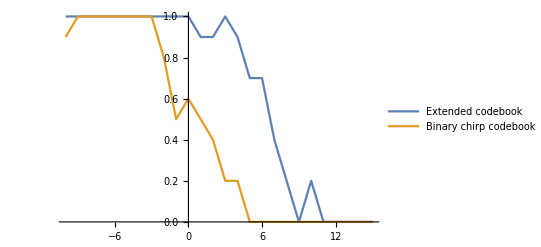

```mathematica
(* COMMUNICATION SCENARIO SIMULATION *)
Timing[
drops = 10;
SNRValues = Range[-10,15,1];
ResultsNew = {};
ResultsOld = {};
(SNR = #;
gamma = 10^(SNR/10);
errors = 0;
(
Smatrix = RandomChoice[ExtendedSmats];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate,bestimate}=ExtendedDecoder[tstvec];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors += 1];
)&/@ Range[drops];
AppendTo[ResultsNew, {SNR, errors/drops//N}];
errors = 0;
(
Smatrix = RandomChoice[AllBinSymm];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate, bestimate, zleft, metric}=BreadthFirstDecoding[tstvec, 1, True, Range[mm]];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors += 1];
)&/@ Range[drops];
AppendTo[ResultsOld, {SNR, errors/drops//N}];
)&/@ SNRValues;]
Print[ResultsNew];
Print[ResultsOld];
ListLinePlot[{ResultsNew, ResultsOld}, PlotLegends->{"Extended codebook", "Binary chirp codebook"}]
```

```mathematica
tstvec = E^(I*2Pi*RandomReal[10, Nn])
tstvec = Transpose[ExtendedCB][[129]]
```

{-0.290286+0.95694 ⅈ,0.308925+0.951086 ⅈ,-0.29536-0.955386 ⅈ,-0.914079-0.405536 ⅈ,-0.737268+0.675601 ⅈ,-0.909964-0.414687 ⅈ,0.271254+0.962508 ⅈ,-0.853811-0.520583 ⅈ}

{1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)}

```mathematica
ExtendedDecoderBf[tstvec, 2] // mf
```

({{0,0,0},{0,0,1},{0,1,0}} | {0,0,0} | {1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)} | 1
{{0,0,0},{0,0,1},{0,1,1}} | {0,0,1/2} | {1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2)} | 1/2
{{0,0,0},{0,0,1},{0,1,2}} | {0,0,1} | {1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2)} | 1
{{0,0,0},{0,0,1},{0,1,1}} | {0,0,1/2} | {1/(4 √2),-ⅈ/(4 √2),1/(4 √2),ⅈ/(4 √2),1/(4 √2),-ⅈ/(4 √2),1/(4 √2),ⅈ/(4 √2)} | 1/2)

({{0,0,0},{0,0,1},{0,1,2}}
{0,0,1}
{1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2)}
1)

{3813.94,Null}

{}

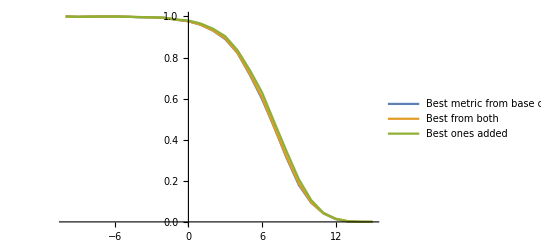

```mathematica
(* DIFFERENT BF ALGOS FOR EXTENDED BCS *)
Timing[
drops = 3000;
SNRValues =  Range[-10,15,1];
ResultsNew = {};
BfResults ={};
BfPlusResults = {};
BfBestBothResults = {};
(SNR = #;
gamma = 10^(SNR/10);
errors = {0,0,0};
(
Smatrix = RandomChoice[ExtendedSmats];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate,bestimate,zleft, metric}=ExtendedDecoderBf[tstvec,2];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[1]] = errors[[1]]+1];

{Sestimate,bestimate,zleft, metric}=ExtendedDecoderBfPlus[tstvec,2];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[2]] = errors[[2]]+1];

{Sestimate,bestimate,zleft, metric}=ExtendedDecoderBfBestBoth[tstvec,2];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[3]] =errors[[3]]+ 1];
)&/@ Range[drops];
errorprobs = errors/drops//N;
AppendTo[BfResults, {SNR, errorprobs[[1]]}];
AppendTo[BfPlusResults, {SNR, errorprobs[[2]]}];
AppendTo[BfBestBothResults, {SNR, errorprobs[[3]]}];
)&/@ SNRValues;]
Print[ResultsNew];
ListLinePlot[{BfResults, BfPlusResults, BfBestBothResults},PlotLegends->{"Best metric from base chirps", "Best from both", "Best ones added"}]
```

```mathematica
ResultsNew
```

{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{0.666667,0.666667,0.666667},{1.,1.,1.},{0.666667,0.666667,0.666667},{0.666667,0.666667,0.666667},{0.333333,0.333333,0.333333},{0.666667,0.333333,0.333333},{0.333333,0.333333,0.333333},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
BfResults
```

{{-10,{1.,1.,1.}},{-9,{1.,1.,1.}},{-8,{1.,1.,1.}},{-7,{1.,1.,1.}},{-6,{1.,1.,1.}},{-5,{1.,1.,1.}},{-4,{1.,1.,1.}},{-3,{1.,1.,1.}},{-2,{1.,1.,1.}},{-1,{1.,1.,1.}},{0,{0.666667,0.666667,1.}},{1,{0.666667,0.666667,0.666667}},{2,{1.,1.,1.}},{3,{1.,1.,1.}},{4,{0.666667,0.666667,1.}},{5,{0.666667,0.666667,1.}},{6,{0.666667,0.666667,1.}},{7,{0.666667,0.666667,0.666667}},{8,{0.333333,0.333333,0.333333}},{9,{0.333333,0.333333,0.333333}},{10,{0.333333,0.333333,0.333333}},{11,{0.,0.,0.}},{12,{0.,0.,0.}},{13,{0.,0.,0.}},{14,{0.,0.,0.}},{15,{0.,0.,0.}}}

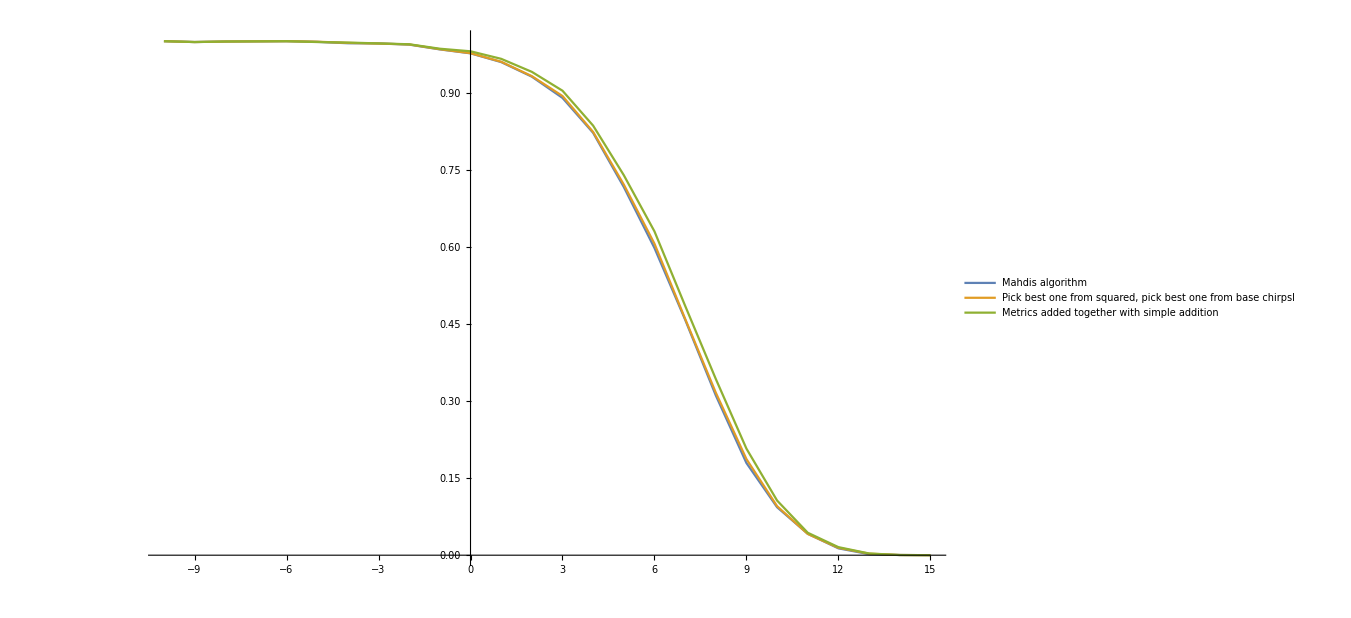

```mathematica
p1 = ListLinePlot[{BfResults, BfPlusResults, BfBestBothResults},PlotLegends->{"Mahdis algorithm", "Pick best one from squared, pick best one from base chirpsl", "Metrics added together with simple addition"}, ImageSize->{1000,1000}]
```

```mathematica
Export["howard.png", p1];
```